```mathematica
Quit;
ClearAll;
```

```mathematica
d=3;
```

```mathematica
L=1;
```

```mathematica
Action=Sqrt[r[x]^(2(d-1))(r[x]^2+2r'[x]v'[x]-(r[x]^2-m[v[x]]/r[x]^(d-1))v'[x]^2)];
```

```mathematica
a=1/3; (*Parameter which controls the speed of the perturbation*)
Subscript[m, 0]=1; (*final value of mass function*)
m[v_]:=Subscript[m, 0](Tanh[v/a]+1)/2; (*define the mass function*)
t=3; (*Inital field theory time on boundary*)
rmax=100;
xmax=100;
```

NDSolve::ndsz: At x == 2.50898, step size is effectively zero; singularity or stiff system suspected.

{{r→                              -10
InterpolatingFunction[{{5.4 10   , 2.50898}}, <>],v→                              -10
InterpolatingFunction[{{5.4 10   , 2.50898}}, <>]}}

rmin= 0.59954

vmin= -0.673669

ℓ/2= 1.69295

x @ vmin 1.69295

x @ rmin 1.65232

derivatives @ ℓ/2{{0.0227059,-1.92271×10^-8}}

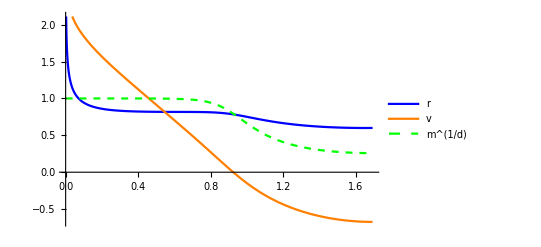

```mathematica
r0=0.6; (*Minimum value of r*)
Eqn1=r[x]^2+2 r'[x] v'[x]-((-m[v[x]])/r[x]^(d-1)+r[x]^2) v'[x]^2-r[x]^(2(d+1))/r0^(2d);
Eqn2=((d-1)r[x]^(2d+1))/r0^(2d)+(2(d+1) r'[x] v'[x])/r[x]+(d+1) r[x](1- v'[x]^2)-2 v''[x];
x0=(1/(d+1)r0^d/rmax^(d+1));
b=0.51735;(*integration const b*)
Sol=NDSolve[{Eqn1==0,Eqn2==0,r[x0]==rmax,v[x0]==t-1/rmax+b/((d+1)rmax^(d+1)),v'[x0]==-(rmax/r0)^d+b/r0^d},{r,v},{x,x0,xmax}]
ℓ=2*x/.Last[Quiet[FindMinimum[v[x]/.Sol,{x,x0,x0,xmax}]]];
Print["rmin= ",rmin=First[Quiet[FindMinimum[r[x]/.Sol,{x,ℓ/2,x0,ℓ/2}]]]]
Print["vmin= ",vmin=First[Quiet[FindMinimum[v[x]/.Sol,{x,ℓ/2,x0,ℓ/2}]]]]
Print["ℓ/2= ",ℓ/2]
Print["x @ vmin ",x/.Last[Quiet[FindMinimum[v[x]/.Sol,{x,ℓ/2,x0,ℓ/2}]]]]
Print["x @ rmin ",x/.Last[Quiet[FindMinimum[r[x]/.Sol,{x,ℓ/2,x0,ℓ/2}]]]]
Print["derivatives @ ℓ/2",{r'[ℓ/2-x0],v'[ℓ/2]}/.Sol]
ab=Plot[{Evaluate[r[x]/.Sol],Evaluate[v[x]/.Sol],Evaluate[m[v[x]]^(1/d)/.Sol]},{x,x0,ℓ/2},PlotStyle->{Blue,Orange,{Dashed,Green}},PlotLegends->{"r","v","m^(1/d)"},AxesOrigin->{0,0}]
```

```mathematica
LInt=(2 L^(d-1))/r0^d*(NIntegrate[r[x]^(2d)/.Sol,{x,x0,ℓ/2}])-(2 L^(d-1))/(d-1)(rmax)^(d-1)
ℓ
```

{2.93004}

3.38589

```mathematica
t1=ListPlot[{{0.288272,-3.81264
},{0.438796,-1.55989},{0.845146,-0.116441},{1.030026,0.120148},{1.306548,0.310811},{1.519178,0.378912},{2.1412,0.458788},{2.6624,0.492996},{2.79032,0.502139},{4.03084,0.517071},{0.215789,-6.86062},{0.609105,-0.669291}},PlotStyle->{Red},AxesOrigin->{0,0}];
t2=ListPlot[{{0.289114,-3.78949},{0.4384688273130787,-1.56041},{0.610226,-0.656607},{0.856978,-0.0550071},{2.37854,1.59931},{2.44932,1.61238},{2.80498,1.61925},{3.58812,1.63529},{5.72796,1.64977},{6.51236,1.65259}},PlotStyle->{Blue},AxesOrigin->{0,0}];
t3=ListPlot[{{0.288363,-3.80974},{0.438469,-1.5604},{0.610228,-0.656573},{0.857014,-0.0548085},{3.93908,2.88},{5.32798,2.88556},{6.37262,2.88834}},PlotStyle->{Green},AxesOrigin->{0,0}];
```

```mathematica
Show[t1,t2,t3,VacRes,TherRes,PlotRange->{{0,10},{-4,5}}]
```

-Graphics-

```mathematica
ac=ParametricPlot3D[{Evaluate[{x,v[x],r[x]}/.Sol]},{x,x0,ℓ/2},AxesLabel->{"x","v","r"},PlotRange->{{x0,ℓ/2},{-8,t},{0.0,2.0}}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[Evaluate[{y,x,r[x]}/.Sol],{x,x0,ℓ/2},{y,x0,10}] (*plot of surface need to reflect *)
```

-Graphics3D-

```mathematica
pq=ParametricPlot3D[Evaluate[{y,v[x],m[v[x]]^(1/d)}/.Sol],{x,x0,ℓ/2},{y,x0,ℓ/2},PlotRange->All]
```

-Graphics3D-

```mathematica
f=Show[{ac,pq},AspectRatio->1/2]
```

-Graphics3D-

```mathematica
Show[f,pq]
```

-Graphics3D-

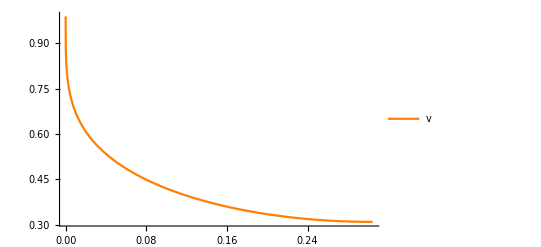

```mathematica
Plot[{Evaluate[v[x]/.Sol]},{x,x0,ℓ/2},PlotRange->All,PlotStyle->{Orange},PlotLegends->{"v"},PlotRange->All]
```

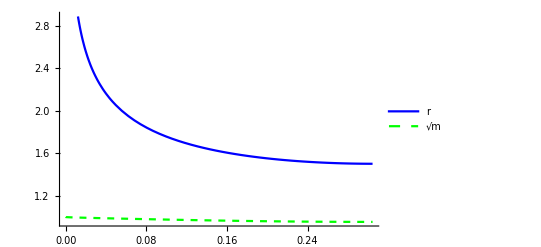

```mathematica
Plot[{Evaluate[r[x]/.Sol],Evaluate[m[v[x]]^(1/d)/.Sol]},{x,x0,ℓ/2},PlotStyle->{Blue,{Dashed,Green}},PlotLegends->{"r","√m"}]
```

```mathematica
Actionbh=Sqrt[r^(2(d-1))(1/(r^2-Subscript[m, 0]/r^(d-1))+r^2 x'[r]^2)];
A[ra_]:=2 L^(d-1)(NIntegrate[Actionbh/.NDSolve[{x'[r]==√(ra^(2d)/(r^2(r^2-Subscript[m, 0]/r^(d-1))(r^(2d)-ra^(2d)))),x[rmax]==0.01},x,{r,ra,rmax}],{r,ra,rmax}])-(2 L^(d-1))/(d-1)(rmax)^(d-1)
q[ra_]:=2*Abs[x[ra]/.NDSolve[{x'[r]==√(ra^(2d)/(r^2(r^2-Subscript[m, 0]/r^(d-1))(r^(2d)-ra^(2d)))),x[rmax]==0.01},x,{r,ra,rmax}]]
TherTable=Quiet[Partition[Flatten[Table[{q[ra],A[ra]},{ra,1,15,0.1}],2],2]];
TherRes=ListCurvePathPlot[{TherTable},PlotRange->{{0,60},{-200,20}},AxesOrigin->{0,0},PlotStyle->{Black,Dashed},InterpolationOrder->2];
VacRes=Plot[(-2^d Pi^(d/2))/(d-1)(L/q)^(d-1)(Gamma[(d+1)/(2d)]/Gamma[1/(2d)])^(d-1),{q,0,60},PlotStyle->{Black, DotDashed},PlotRange->{{0,60},{-200,10}}];
```

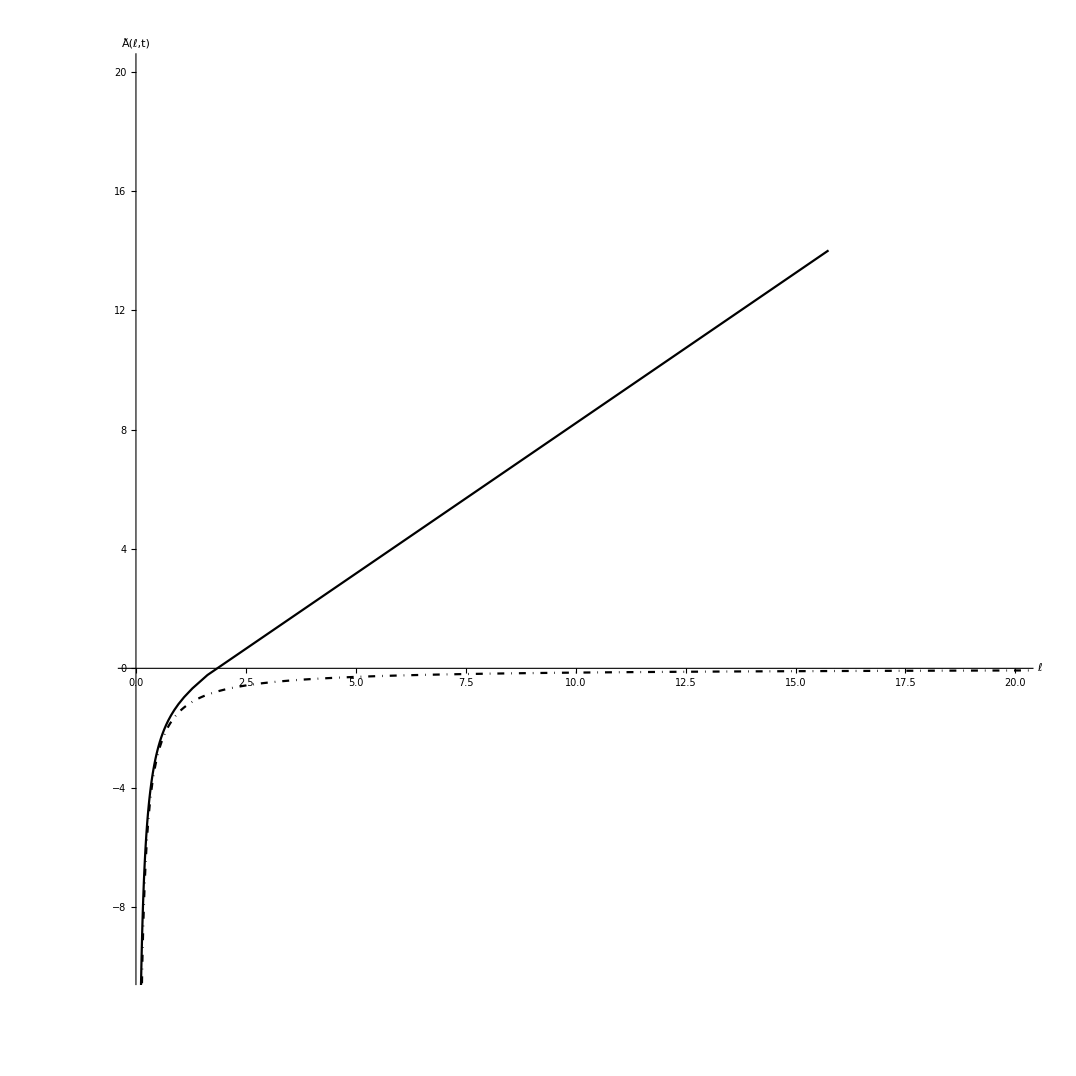

```mathematica
Show[{VacRes,TherRes},PlotRange->{{0,20},{-10,20}},AxesLabel->{"ℓ","Ã(ℓ,t)"},AspectRatio->1]
```